```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v4

```mathematica
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,960,1200,10}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,960,1200,10}];
r422=chi4/chi2;
```

```mathematica
mub=Table[i,{i,960,1200,10}];
T=Table[i,{i,1,17,1}];
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],r42[[j]][[i]]},{i,1,Length[T]},{j,1,Length[mub]}],1];
Export["r42high2.dat",R42all]
```

r42high2.dat

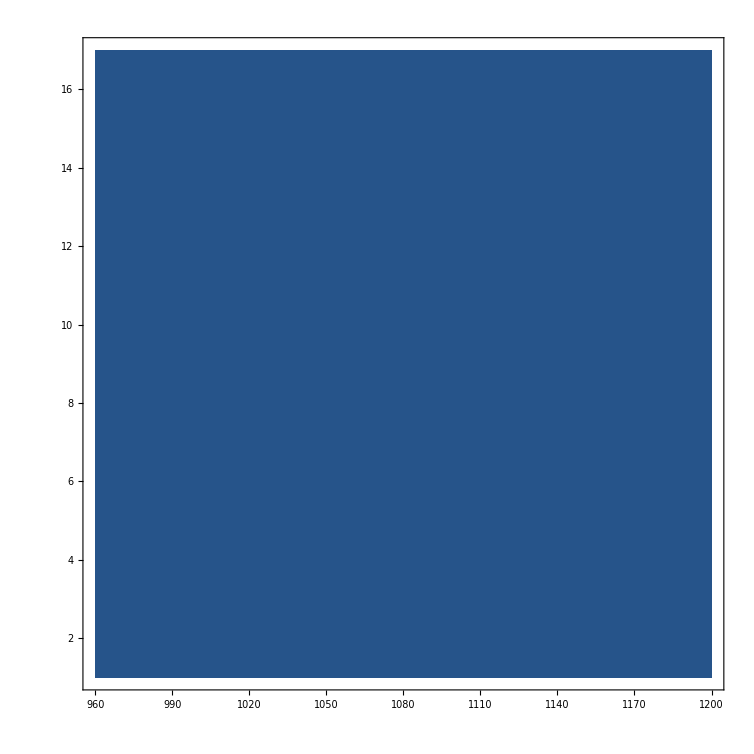

```mathematica
ListDensityPlot[R42all,PlotRange->{All,All,{-5,5}}]
```

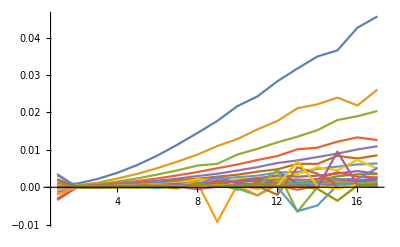

```mathematica
ListLinePlot[r422,PlotRange->{All,All}]
```